```mathematica
<<"/Users/ethan/Desktop/WSS2017/saved_data/editInfo.mx"
<<"/Users/ethan/Desktop/WSS2017/saved_data/compData.mx"
```

```mathematica
template ={"https://tools.wmflabs.org/xtools-articleinfo/?article=","&project=en.wikipedia.org"};
urlForm = Flatten @ Table[StringReplace[i, " "-> "_"], {i, Keys[compData]}];
TitleToEdit[article_] :=Block[{}, 
	(*Print[template[[1]]<> article <> template[[2]]]; *)
	Import[template[[1]]<> article <> template[[2]], "Data"]
]
```

```mathematica
editInfo = AssociationMap[TitleToEdit, urlForm];
```

```mathematica
DumpSave["/Users/ethan/Desktop/WSS2017/saved_data/editInfo.mx",editInfo];
```

```mathematica
TotalRevisions[article_]:= editInfo[article][[2]][[1]][[1]][[4]][[2]]
NumEditors[article_]:=N[editInfo[article][[2]][[1]][[1]][[5]][[2]]]
```

```mathematica
revCount = AssociationMap[Replace[s_String:>ToExpression@StringDelete[s,","]]@*TotalRevisions,urlForm];
editorCount = AssociationMap[NumEditors,urlForm];
revPerEditor=Sort[revCount/editorCount,Greater];
```

```mathematica
Histogram[#,{50},ImageSize-> Large,PlotRange->Automatic]&/@{revCount,editorCount,{revCount,editorCount}}//Row;
Histogram[revPerEditor,{0.5},ImageSize->Large,PlotRange->All];
```

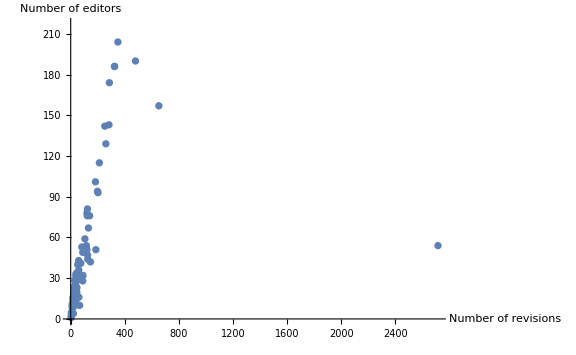

```mathematica
revEditList = Table[{revCount[[i]],editorCount[[i]]},{i,Length[revCount]}];
ListPlot[Tooltip[revEditList],LabelingFunction->None,AxesLabel->{"Number of revisions","Number of editors"},PlotRange->{All,Automatic},ImageSize->Large]
```

```mathematica
editInfo["Computational_X"][[2]][[3]][[1]][[2;;]]
```

{{Pleasantville, ec · topedits ,2,0,0 %,2016-11-15, 15:30,2016-11-15, 16:34,0,1,610},{Missionedit, ec · topedits ,1,1,100 %,2016-11-15, 18:23,2016-11-15, 18:23,0,1}}

```mathematica
EditorStats[article_]:=
	If[
		Length@editInfo[article][[2]][[3]][[1]][[2;;]] ≤ 30,
		{Table[
			editInfo[article][[2]][[3]][[1]][[i]][[3]], {i, 2, Length@editInfo[article][[2]][[3]][[1]]}
		],
		Table[
			editInfo[article][[2]][[3]][[1]][[i]][[1]], {i, 2, Length@editInfo[article][[2]][[3]][[1]]}
		]},
		{Table[
			editInfo[article][[2]][[3]][[1]][[i]][[3]], {i, 2, 30}
		],
		Table[
			editInfo[article][[2]][[3]][[1]][[i]][[1]], {i, 2, 30}
		],
		editInfo[article][[2]][[3]][[1]][[32]]
		}
	]
```

```mathematica
editStats = AssociationMap[EditorStats,urlForm];
```

```mathematica
editStats["Computational_biology"]
```

{{14,10,10,9,7,6,6,6,6,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,2,2},{Manuelcorpas,Alexbateman,Mim.cis,Rjwilmsi,Pbowen91,U+003F,JustinClarkCasey,Jethero,Marcoacostareyes,Guillaume2303,139.80.7.229,112.198.68.233,Download,Pchanda2,Zuck3434,JASONKEIL,Favrin,ClueBot NG,Dratman,SmackBot,Kku,71.58.41.225,Gupta.udatha,Duncan.Hull,Ppgardne,220.225.236.50,82.31.186.210,Monkbot,EmausBot},{174 others,208,-More-}}

```mathematica
Total@editStats["Computational_biology"][[1]]
```

139

```mathematica
PlotEditStats[article_] :=PieChart[editStats[article][[1]]]
```